# Основы языка Wolfram

## Самостоятельная работа 5. Функциональное программирование

Вариант 1

Используя функцию Graph напишите свою функцию, которая генерирует полный двудольный граф с заданным количеством вершин в каждой из долей (k_1 и k_2). На приведенном рисунке k_1=6, k_2=4. Указание:  для правильного отображения двудольного графа используйте опцию GraphLayout.

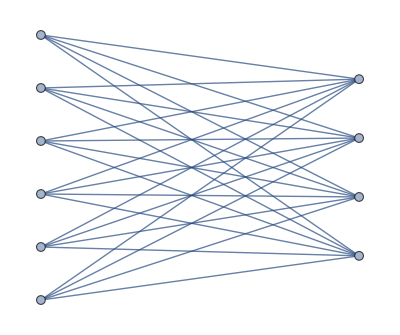

Задание нужно выполнить двумя способами: а) как-нибудь, б) с помощью функции Outer.

Вариант 2

Используя функцию Outer, напишите свою функцию, которая умножает две матрицы. В случае, если размерности матриц не совместимы, необходимо выдавать сообщение об ошибке.

Напишите функцию, которая вычисляет дивергенцию вектор-функции. На вход подается вектор-функция в виде списка и список переменных, от которых она зависит. Указание: используйте функцию Inner.

Вариант 3

Напишите функцию, которая принимает на вход список функций fs={f1,f2,...,fn} и список переменных xs={x1,x2,...xn}, и возвращает список {f1[x1],f2[x2],...,fn[xn]}. В случае несовпадения длин списков выражение должно возвращаться в исходном (невычисленном) виде. Реализовать данную функцию нужно четырьмя способами:
1. С помощью Inner. 2. С помощью Thread. 3. С помощью MapThread. 4. Еще каким-нибудь способом.

Дан список коэффициентов {a_n, a_(n-1),.., a_1, a_0}. Написать функцию, которая возвращает многочлен с этими коэффициентами, записанный по схеме Горнера, от указанной переменной x. Указание:  используйте функцию Fold.

```mathematica
poly[{a,b,c,d,e},x]
```

e+x (d+x (c+x (b+a x)))